```mathematica
a1={1,1,1,1};
a2={1,-1,1,-1};
a3={1,1,-1,-1};
a4={-1,1,1,-1};
V={a1,a2,a3,a4}
G4[{α1_,α2_,α3_,α4_}]:=V.DiagonalMatrix[{α1,α2,α3,α4}].Vᵀ
Eigenvalues[G4[{α1,α2,α3,α4}]]
MatrixForm[G4[{α1,α2,α3,α4}]]
Hmm=G4[{α1,α2,α3,α4}]⟦1⟧
Eqs=Table[p[i]==Hmm⟦i⟧,{i,4}]
Solve[Eqs,{α1,α2,α3,α4}]
```

{{1,1,1,1},{1,-1,1,-1},{1,1,-1,-1},{-1,1,1,-1}}

{4 α1,4 α2,4 α3,4 α4}

(α1+α2+α3+α4 | α1-α2+α3-α4 | α1+α2-α3-α4 | -α1+α2+α3-α4
α1-α2+α3-α4 | α1+α2+α3+α4 | α1-α2-α3+α4 | -α1-α2+α3+α4
α1+α2-α3-α4 | α1-α2-α3+α4 | α1+α2+α3+α4 | -α1+α2-α3+α4
-α1+α2+α3-α4 | -α1-α2+α3+α4 | -α1+α2-α3+α4 | α1+α2+α3+α4)

{α1+α2+α3+α4,α1-α2+α3-α4,α1+α2-α3-α4,-α1+α2+α3-α4}

{p[1]==α1+α2+α3+α4,p[2]==α1-α2+α3-α4,p[3]==α1+α2-α3-α4,p[4]==-α1+α2+α3-α4}

{{α1→1/4 (p[1]+p[2]+p[3]-p[4]),α2→1/4 (p[1]-p[2]+p[3]+p[4]),α3→1/4 (p[1]+p[2]-p[3]+p[4]),α4→1/4 (p[1]-p[2]-p[3]-p[4])}}

## Finding G2’s: Simples

### G2: Type 1 and 2

The standard G2 is 
	Q=(p1 | p2
-p2 | p1)
a less standard but no less orthogonal Q is
	 Q=(p1 | p2
p2 | -p1)

```mathematica
G2[1][{p1_,p2_}]:={{p1,p2},{-p2,p1}}
G2[2][{p1_,p2_}]:={{p1,p2},{p2,-p1}}
```

Checking that both versions satisfy the appropriate identity

```mathematica
Clear[p1,p2,Q1,Q2]
{Q1,Q2}={G2[1][{p1,p2}],G2[2][{p1,p2}]};
Map[ Norm[#.#ᵀ-Total[{p1,p2}^2] IdentityMatrix[2]]&,{Q1,Q2}]
```

{0,0}

Note that the eigenvectors of G2[1] are independent of {p1,p2} while those of G2[2] are not.

```mathematica
Clear[p1,p2,p3,p4,Q1,Q2]
{Q1,Q2}={G2[1][{p1,p2}],G2[2][{p1,p2}]};
Map[Eigenvectors,{Q1,Q2}]
```

{{{ⅈ,1},{-ⅈ,1}},{{-(-p1+√(p1^2+p2^2))/p2,1},{-(-p1-√(p1^2+p2^2))/p2,1}}}

This means that G2[1][{p1,p2}] commutes with G2[1][{p3,p4}] (and transposes etc) for any values of the arguments {p1,p2,p3,p4},

```mathematica
Clear[p1,p2,p3,p4]
{Q1,Q2}={G2[1][{p1,p2}],G2[1][{p3,p3}]};
{Q1ᵀ.Q2==Q2.Q1ᵀ,Q1.Q2==Q2.Q1}
```

{True,True}

## Finding G4’s: Brute Force and ignorance

### G4: Type 1

One type of G4 looks like 
	Q=(p1 | p2 | p3 | p4
-p2 | p1 | -x | -y
-p3 | +x | p1 | -z
-p4 | +y | +z | p1)
where {x,y,z} is some permutation of {p2,p3,p4} with some minus signs scattered in.  I can get Mma to find two of these.

```mathematica
Clear[x,y,z,Q,p1,p2,p3,p4]
Q={{p1,p2,p3,p4},
{-p2,p1,-x,-y},
{-p3,x,p1,-z},
{-p4,y,z,p1}};
QQt=Q.Qᵀ;
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]];
Solve[Eqs,{x,y,z}]
```

{{x→-p4,y→p3,z→-p2},{x→p4,y→-p3,z→p2}}

Defining these two types.

```mathematica
{G4[1][{p1_,p2_,p3_,p4_}],G4[2][{p1_,p2_,p3_,p4_}]}={({{p1, p2, p3, p4}, {-p2, p1, -p4, p3}, {-p3, p4, p1, -p2}, {-p4, -p3, p2, p1}}), ({{p1, p2, p3, p4}, {-p2, p1, p4, -p3}, {-p3, -p4, p1, p2}, {-p4, p3, -p2, p1}})};
```

The first variant here is

```mathematica
Q11A =G2[1][{p1,p2}];
Q22A=Q11Aᵀ;
Q12A=G2[1][{p3,p4}];
Q21A=-Q12Aᵀ;
Q4A=ArrayFlatten[({{Q11A, Q12A}, {Q21A, Q22A}})];
MatrixForm[Q4A-G4[1][{p1,p2,p3,p4}]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Q11B =G2[1][{p1,p2}];
Q22B=Q11B;
Q12B=G2[2][{p3,p4}];
Q21B=-Q12Bᵀ;
Q4B=ArrayFlatten[({{Q11B, Q12B}, {Q21B, Q22B}})];
MatrixForm[Q4B-G4[2][{p1,p2,p3,p4}]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

The eigenvectors are NOT independent of the parameters!

```mathematica
Map[Simplify[Eigenvectors[#]]&,{G4[1][{p1,p2,p3,p4}],G4[2][{p1,p2,p3,p4}]}]
```

{{{(-p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0},{-(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0}},{{(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(-p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0},{(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{-(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0}}}

### G4: Type 2

Another type of G4 looks like 
	Q=(p1 | p2 | p3 | p4
p2 | -p1 | -x | -y
p3 | +x | -p1 | -z
p4 | +y | +z | -p1)
where {x,y,z} is some permutation of {p2,p3,p4} with some minus signs scattered in.  I can get Mathematica to find two of these as well.

```mathematica
Ps={{p4,-p3,p2},{-p4,p3,-p2}};
Table[
{x,y,z}=ps;
Q={{p1,p2,p3,p4},
{p2,-p1,-x,-y},
{p3,x,-p1,-z},
{p4,y,z,-p1}};
If[Q.Qᵀ ===(p1^2+p2^2+p3^2+p4^2)IdentityMatrix[4],MatrixForm[Q],Null] ,
{ps,Ps}]
```

{(p1 | p2 | p3 | p4
p2 | -p1 | -p4 | p3
p3 | p4 | -p1 | -p2
p4 | -p3 | p2 | -p1),(p1 | p2 | p3 | p4
p2 | -p1 | p4 | -p3
p3 | -p4 | -p1 | p2
p4 | p3 | -p2 | -p1)}

Defining these two new types.  These two new ones are not rotations since they have determinant -1 rather than 1.

```mathematica
{G4[3][{p1_,p2_,p3_,p4_}],G4[4][{p1_,p2_,p3_,p4_}]}={({{p1, p2, p3, p4}, {p2, -p1, -p4, p3}, {p3, p4, -p1, -p2}, {p4, -p3, p2, -p1}}), ({{p1, p2, p3, p4}, {p2, -p1, p4, -p3}, {p3, -p4, -p1, p2}, {p4, p3, -p2, -p1}})};
```

```mathematica
p=Normalize[RandomReal[{-1,1},4]];
Map[Det,Table[G4[i][p],{i,4}]]
Map[Eigenvalues,Table[G4[i][p],{i,4}]]
```

{1.,1.,-1.,-1.}

{{0.367164+0.930156 ⅈ,0.367164-0.930156 ⅈ,0.367164+0.930156 ⅈ,0.367164-0.930156 ⅈ},{0.367164+0.930156 ⅈ,0.367164-0.930156 ⅈ,0.367164+0.930156 ⅈ,0.367164-0.930156 ⅈ},{-1.+0. ⅈ,-0.367164+0.930156 ⅈ,-0.367164-0.930156 ⅈ,1.+0. ⅈ},{-0.367164+0.930156 ⅈ,-0.367164-0.930156 ⅈ,-1.+0. ⅈ,1.+0. ⅈ}}

How are these built from the smaller ones?

```mathematica
Clear[p1,p2,p3,p4]
Q11C=G2[2][{p1,p2}];
Q22C=-G2[1][{p1,p2}];
Q12C=G2[1][{p3,p4}];
Q21C=G2[2][{p3,p4}];
Q4C=ArrayFlatten[({{Q11C, Q12C}, {Q21C, Q22C}})];
MatrixForm[G4[3][{p1,p2,p3,p4}]-Q4C]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Q11D=G2[2][{p1,p2}];
Q22D=-G2[1][{p1,p2}]ᵀ;
Q12D=G2[2][{p3,p4}];
Q21D=G2[1][{p3,p4}]ᵀ;
Q4D=ArrayFlatten[({{Q11D, Q12D}, {Q21D, Q22D}})];
MatrixForm[G4[4][{p1,p2,p3,p4}]-Q4D]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

I have two kinds of G2:  One Rotations and One Reflection.  The products come in two pairs. Diagonal and off-diagonal

```mathematica
TableForm[
Table[
A=G2[i][{p1,p2}];
B=G2[j][{p3,p4}];
MatrixForm[Aᵀ.B],
{i,2},{j,2}]
]
```

(p1 p3+p2 p4 | -p2 p3+p1 p4
p2 p3-p1 p4 | p1 p3+p2 p4) | (p1 p3-p2 p4 | p2 p3+p1 p4
p2 p3+p1 p4 | -p1 p3+p2 p4)
(p1 p3-p2 p4 | p2 p3+p1 p4
p2 p3+p1 p4 | -p1 p3+p2 p4) | (p1 p3+p2 p4 | -p2 p3+p1 p4
p2 p3-p1 p4 | p1 p3+p2 p4)

The eigenvectors are NOT independent of the parameters!

```mathematica
Map[Simplify[Eigenvectors[#]]&,{G4[3][{p1,p2,p3,p4}],G4[4][{p1,p2,p3,p4}]}]
```

{{{(p1-√(p1^2+p2^2+p3^2+p4^2))/p4,p2/p4,p3/p4,1},{(p1+√(p1^2+p2^2+p3^2+p4^2))/p4,p2/p4,p3/p4,1},{0,((p3^2+p4^2) (p1+√(-p2^2-p3^2-p4^2)))/(p2^2 p3-p2 p4 (p1+√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2-p1 √(-p2^2-p3^2-p4^2))),(p1 p2 p3+p2^2 p4+p3^2 p4+p4^3+p2 p3 √(-p2^2-p3^2-p4^2)-p1 p4 √(-p2^2-p3^2-p4^2))/(-p2^2 p3+p2 p4 (p1+√(-p2^2-p3^2-p4^2))-p3 (p3^2+p4^2-p1 √(-p2^2-p3^2-p4^2))),1},{0,-((p3^2+p4^2) (-p1+√(-p2^2-p3^2-p4^2)))/(p2^2 p3+p2 p4 (-p1+√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2+p1 √(-p2^2-p3^2-p4^2))),-(p1 p2 p3+p2^2 p4+p3^2 p4+p4^3-p2 p3 √(-p2^2-p3^2-p4^2)+p1 p4 √(-p2^2-p3^2-p4^2))/(p2^2 p3+p2 p4 (-p1+√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2+p1 √(-p2^2-p3^2-p4^2))),1}},{{(p1-√(p1^2+p2^2+p3^2+p4^2))/p4,p2/p4,p3/p4,1},{(p1+√(p1^2+p2^2+p3^2+p4^2))/p4,p2/p4,p3/p4,1},{0,-((p3^2+p4^2) (p1+√(-p2^2-p3^2-p4^2)))/(p2^2 p3+p2 p4 (p1+√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2-p1 √(-p2^2-p3^2-p4^2))),(-p2^2 p4+p2 p3 √(-p2^2-p3^2-p4^2)-p4 (p3^2+p4^2)+p1 (p2 p3+p4 √(-p2^2-p3^2-p4^2)))/(p2^2 p3+p2 p4 (p1+√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2-p1 √(-p2^2-p3^2-p4^2))),1},{0,((p3^2+p4^2) (-p1+√(-p2^2-p3^2-p4^2)))/(p2^2 p3+p2 p4 (p1-√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2+p1 √(-p2^2-p3^2-p4^2))),-(-p1 p2 p3+p2^2 p4+p3^2 p4+p4^3+p2 p3 √(-p2^2-p3^2-p4^2)+p1 p4 √(-p2^2-p3^2-p4^2))/(p2^2 p3+p2 p4 (p1-√(-p2^2-p3^2-p4^2))+p3 (p3^2+p4^2+p1 √(-p2^2-p3^2-p4^2))),1}}}

```mathematica
Clear[p1,p2,p3,p4]
TableForm[
Map[Simplify[Eigenvalues[#]]&,{G4[1][{p1,p2,p3,p4}],G4[2][{p1,p2,p3,p4}],G4[3][{p1,p2,p3,p4}],G4[4][{p1,p2,p3,p4}]}]
]
```

p1-√(-p2^2-p3^2-p4^2) | p1-√(-p2^2-p3^2-p4^2) | p1+√(-p2^2-p3^2-p4^2) | p1+√(-p2^2-p3^2-p4^2)
p1-√(-p2^2-p3^2-p4^2) | p1-√(-p2^2-p3^2-p4^2) | p1+√(-p2^2-p3^2-p4^2) | p1+√(-p2^2-p3^2-p4^2)
-√(p1^2+p2^2+p3^2+p4^2) | √(p1^2+p2^2+p3^2+p4^2) | -p1-√(-p2^2-p3^2-p4^2) | -p1+√(-p2^2-p3^2-p4^2)
-√(p1^2+p2^2+p3^2+p4^2) | √(p1^2+p2^2+p3^2+p4^2) | -p1-√(-p2^2-p3^2-p4^2) | -p1+√(-p2^2-p3^2-p4^2)

```mathematica
Map[Simplify[Eigenvectors[#]]&,{G4[1][{p1,p2,p3,p4}],G4[2][{p1,p2,p3,p4}]}]
```

{{{(-p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0},{-(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0}},{{(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4-p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{(-p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3+p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0},{(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),0,1},{-(p2 p4+p3 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),(p2 p3-p4 √(-p2^2-p3^2-p4^2))/(p3^2+p4^2),1,0}}}

```mathematica
p=Normalize[RandomReal[{-1,1},4]];
TableForm[
Map[Eigenvalues,{G4[1][p],G4[2][p],G4[3][p],G4[4][p]}],
TableHeadings->Automatic
]
TableForm[
Chop[Map[Eigenvectors,{G4[1][p],G4[2][p],G4[3][p],G4[4][p]}]],
TableHeadings->Automatic
]
```

| 1 | 2 | 3 | 4
1 | 0.125991+0.992031 ⅈ | 0.125991-0.992031 ⅈ | 0.125991+0.992031 ⅈ | 0.125991-0.992031 ⅈ
2 | 0.125991+0.992031 ⅈ | 0.125991-0.992031 ⅈ | 0.125991+0.992031 ⅈ | 0.125991-0.992031 ⅈ
3 | -1.+0. ⅈ | -0.125991+0.992031 ⅈ | -0.125991-0.992031 ⅈ | 1.+0. ⅈ
4 | -1.+0. ⅈ | -0.125991+0.992031 ⅈ | -0.125991-0.992031 ⅈ | 1.+0. ⅈ

| 1 | 2 | 3 | 4
1 | 1 | -0.659116
2 | -0.0769168-0.44226 ⅈ
3 | 0.240619-0.228735 ⅈ
4 | -0.041867-0.502082 ⅈ | 1 | -0.659116
2 | -0.0769168+0.44226 ⅈ
3 | 0.240619+0.228735 ⅈ
4 | -0.041867+0.502082 ⅈ | 1 | -0.235984+0.0307083 ⅈ
2 | 0.138895-0.516212 ⅈ
3 | -0.631049
4 | 0.163697+0.482268 ⅈ | 1 | -0.235984-0.0307083 ⅈ
2 | 0.138895+0.516212 ⅈ
3 | -0.631049
4 | 0.163697-0.482268 ⅈ
2 | 1 | 0.707107
2 | 0.+0.596639 ⅈ
3 | 0.+0.24164 ⅈ
4 | 0.+0.29263 ⅈ | 1 | 0.707107
2 | 0.-0.596639 ⅈ
3 | 0.-0.24164 ⅈ
4 | 0.-0.29263 ⅈ | 1 | 0.0898006+0.0357531 ⅈ
2 | 0.170134+0.393907 ⅈ
3 | -0.669802
4 | 0.119814-0.586139 ⅈ | 1 | 0.0898006-0.0357531 ⅈ
2 | 0.170134-0.393907 ⅈ
3 | -0.669802
4 | 0.119814+0.586139 ⅈ
3 | 1 | -0.661063
2 | 0.63311
3 | 0.25641
4 | 0.310517 | 1 | 0
2 | -0.21695+0.311375 ⅈ
3 | 0.664538
4 | -0.106406-0.634859 ⅈ | 1 | 0
2 | -0.21695-0.311375 ⅈ
3 | 0.664538
4 | -0.106406+0.634859 ⅈ | 1 | 0.75033
2 | 0.557789
3 | 0.225905
4 | 0.273575
4 | 1 | -0.661063
2 | 0.63311
3 | 0.25641
4 | 0.310517 | 1 | 0
2 | -0.21695-0.311375 ⅈ
3 | 0.664538
4 | -0.106406+0.634859 ⅈ | 1 | 0
2 | -0.21695+0.311375 ⅈ
3 | 0.664538
4 | -0.106406-0.634859 ⅈ | 1 | -0.75033
2 | -0.557789
3 | -0.225905
4 | -0.273575

## Finding G8’s

There is a G8 it looks like this 
	Q=(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | p6 | -p5 | -p8 | p7
-p3 | -p4 | p1 | p2 | p7 | p8 | -p5 | -p6
-p4 | p3 | -p2 | p1 | p8 | -p7 | p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | -p8 | p7 | -p2 | p1 | -p4 | p3
-p7 | p8 | p5 | -p6 | -p3 | p4 | p1 | -p2
-p8 | -p7 | p6 | p5 | -p4 | -p3 | p2 | p1)
I am pretty sure there are lots of others.  This one has G4[2] embedded in the top corner. In particular, I should certainly be able to find one with the G4[1] in the top corner.

```mathematica
Q=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}});
Q.Qᵀ
```

{{p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0,0,0,0,0},{0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0,0,0,0},{0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0,0,0},{0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0,0},{0,0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0},{0,0,0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0},{0,0,0,0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0},{0,0,0,0,0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2}}

```mathematica
Q=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}})
```

```mathematica
QNew=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, -p4, p3, p6, -p5, -p8, p7}, {-p3, p4, p1, -p2, p7, p8, -p5, -p6}, {-p4, -p3, p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, p2, p1, p4, -p3}, {-p7, p8, p5, -p6, p3, -p4, p1, p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}});
QNewᵀ.QNew
```

{{p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,0,-2 p2 p6-2 p3 p7,2 p4 p7,-2 p4 p6,2 p3 p6-2 p2 p7},{0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,0,2 p2 p5+2 p4 p7,2 p3 p7,-2 p3 p6,-2 p4 p6+2 p2 p8},{0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,2 p3 p5-2 p4 p6,-2 p2 p7,2 p2 p6,-2 p4 p7+2 p3 p8},{0,0,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,-2 p3 p5+2 p4 p6-2 p2 p8,2 p2 p5+2 p4 p7-2 p3 p8,0},{-2 p2 p6-2 p3 p7,2 p2 p5+2 p4 p7,2 p3 p5-2 p4 p6,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,2 p1 p2,2 p1 p3,0},{2 p4 p7,2 p3 p7,-2 p2 p7,-2 p3 p5+2 p4 p6-2 p2 p8,2 p1 p2,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,0,-2 p1 p3},{-2 p4 p6,-2 p3 p6,2 p2 p6,2 p2 p5+2 p4 p7-2 p3 p8,2 p1 p3,0,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2,2 p1 p2},{2 p3 p6-2 p2 p7,-2 p4 p6+2 p2 p8,-2 p4 p7+2 p3 p8,0,0,-2 p1 p3,2 p1 p2,p1^2+p2^2+p3^2+p4^2+p5^2+p6^2+p7^2+p8^2}}

```mathematica
Clear[Q,p1,p2,p3,p4,p5,p6,p7,p8]
Q=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}});
Q11=G4[2][{p1,p2,p3,p4}];
Q22=G4[1][{p1,p2,p3,p4}];
Q12=G4[3][{p5,p6,p7,p8}];
Q21=-G4[4][{p5,p6,p7,p8}];
OldQ=ArrayFlatten[({{Q11, Q12}, {Q21, Q22}})];
pSq=Total[{p1,p2,p3,p4,p5,p6,p7,p8}^2]; Id=IdentityMatrix[8];
Map[Norm,{OldQ-Q,Qᵀ.Q-pSq*Id}]
NewQ=ArrayFlatten[({{G4[1][{p1,p2,p3,p4}], G4[4][{p5,p6,p7,p8}]}, {-G4[3][{p5,p6,p7,p8}], G4[2][{p1,p2,p3,p4}]}})];
Map[MatrixForm,{NewQ,NewQ-Q,NewQᵀ.NewQ-pSq *Id}]
```

{0,0}

{(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | -p4 | p3 | p6 | -p5 | p8 | -p7
-p3 | p4 | p1 | -p2 | p7 | -p8 | -p5 | p6
-p4 | -p3 | p2 | p1 | p8 | p7 | -p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | p8 | -p7 | -p2 | p1 | p4 | -p3
-p7 | -p8 | p5 | p6 | -p3 | -p4 | p1 | p2
-p8 | p7 | -p6 | p5 | -p4 | p3 | -p2 | p1),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 p4 | 2 p3 | 0 | 0 | 2 p8 | -2 p7
0 | 2 p4 | 0 | -2 p2 | 0 | -2 p8 | 0 | 2 p6
0 | -2 p3 | 2 p2 | 0 | 0 | 2 p7 | -2 p6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 p8 | -2 p7 | 0 | 0 | 2 p4 | -2 p3
0 | -2 p8 | 0 | 2 p6 | 0 | -2 p4 | 0 | 2 p2
0 | 2 p7 | -2 p6 | 0 | 0 | 2 p3 | -2 p2 | 0),(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)}

```mathematica
Q8Old[{p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_}]:=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}})
Q8New[{p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_}]:=({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, -p4, p3, p6, -p5, p8, -p7}, {-p3, p4, p1, -p2, p7, -p8, -p5, p6}, {-p4, -p3, p2, p1, p8, p7, -p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, p8, -p7, -p2, p1, p4, -p3}, {-p7, -p8, p5, p6, -p3, -p4, p1, p2}, {-p8, p7, -p6, p5, -p4, p3, -p2, p1}})
p=Normalize[RandomReal[{-1,1},8]]
Hmm=Q8New[p];
Hmm=Q8Old[p];
{U,S,V}=SingularValueDecomposition[Hmm];
MatrixForm[V]
```

{-0.563764,0.0471245,0.120552,0.578482,-0.445729,0.103354,0.091642,0.336186}

(0.526113 | -0.174323 | -0.463059 | 0.0741558 | -0.563764 | -0.247562 | -0.0677401 | -0.298644
-0.208215 | 0.303727 | -0.120611 | 0.594514 | 0.0471245 | 0.24045 | 0.329563 | -0.572498
0.131791 | -0.813683 | 0.140691 | 0.0015217 | 0.120552 | 0.392426 | 0.335733 | -0.139665
0.107115 | -0.0173585 | -0.553793 | -0.0528722 | 0.578482 | -0.364682 | 0.431923 | 0.156689
0.0735218 | 0.141469 | 0.266815 | 0.144692 | -0.445729 | -0.115004 | 0.683572 | 0.450871
-0.13108 | -0.282847 | 0.432636 | 0.308615 | 0.103354 | -0.74542 | -0.074235 | -0.220353
0.282892 | 0.285084 | 0.334654 | -0.605942 | 0.091642 | -0.0800566 | 0.290893 | -0.510014
0.740536 | 0.18355 | 0.272381 | 0.393589 | 0.336186 | 0.136454 | -0.173567 | 0.164458)

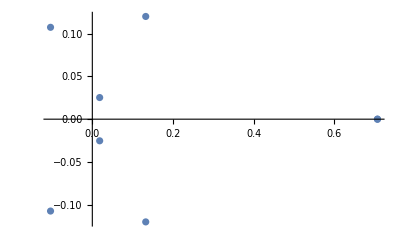

```mathematica
ListPlot[ReIm[V⟦All,1⟧]]
```

```mathematica
Abs[0.22634603461658592-0.4187596799406912 ⅈ]
```

0.476017

```mathematica
1./√2
```

0.707107

```mathematica
Chop[ConjugateTranspose[V].V]
```

{{1.11043,0.0235806,0.191977,0.087437,0.162518,0.197255,0.138999,0.0602385},{0.0235806,0.782223,-0.277721,0.0811794,0.0609763,0.0158611,0.0465251,0.0601602},{0.191977,-0.277721,1.19042,-0.156083,-0.240957,0.253648,-0.096188,0.132322},{0.087437,0.0811794,-0.156083,1.00769,0.0642682,-0.0671314,0.0774949,-0.00849157},{0.162518,0.0609763,-0.240957,0.0642682,1.23182,0.153487,0.230808,0.16324},{0.197255,0.0158611,0.253648,-0.0671314,0.153487,1.13108,0.207247,-0.0364656},{0.138999,0.0465251,-0.096188,0.0774949,0.230808,0.207247,0.657811,-0.0821992},{0.0602385,0.0601602,0.132322,-0.00849157,0.16324,-0.0364656,-0.0821992,0.888527}}

A G8 should look like the

```mathematica
Clear[x,p1,p2,p3,p4,p5,p6,p7,p8]
Q8=Table[x[i,j],{i,8},{j,8}];
Q8⟦1⟧={p1,p2,p3,p4,p5,p6,p7,p8};
Do[Q8⟦i,i⟧=p1,{i,8}];
Q8⟦2;;8,1⟧=-{p2,p3,p4,p5,p6,p7,p8};
Q8⟦1;;4,1;;4⟧=G4[2][{p1,p2,p3,p4}];
Q8=Q8/.x[i_,j_]:>If[i<j,-x[j,i],x[i,j]];
(*{x[5,2],x[6,2]}={p6,-p5};*)
(*{x[7,2],x[8,2]}={p8,-p7};*)
(*{x[5,3],x[6,3]}={p6,-p5};*)
(*{x[7,3],x[8,3]}={p8,-p7};*)
MatrixForm[Q8]
QQt=Q8.Q8ᵀ;
MatrixForm[QQt⟦1;;5,1;;5⟧];
```

(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | -x[5,2] | -x[6,2] | -x[7,2] | -x[8,2]
-p3 | -p4 | p1 | p2 | -x[5,3] | -x[6,3] | -x[7,3] | -x[8,3]
-p4 | p3 | -p2 | p1 | -x[5,4] | -x[6,4] | -x[7,4] | -x[8,4]
-p5 | x[5,2] | x[5,3] | x[5,4] | p1 | -x[6,5] | -x[7,5] | -x[8,5]
-p6 | x[6,2] | x[6,3] | x[6,4] | x[6,5] | p1 | -x[7,6] | -x[8,6]
-p7 | x[7,2] | x[7,3] | x[7,4] | x[7,5] | x[7,6] | p1 | -x[8,7]
-p8 | x[8,2] | x[8,3] | x[8,4] | x[8,5] | x[8,6] | x[8,7] | p1)

```mathematica
vars=Flatten[Table[x[i,j],{i,5,8},{j,2,i-1}]];
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]];
vars⟦1;;10⟧
TableForm[Eqs⟦1;;3⟧]
TableForm[Eqs⟦4;;7⟧]
```

{x[5,2],x[5,3],x[5,4],x[6,2],x[6,3],x[6,4],x[6,5],x[7,2],x[7,3],x[7,4]}

-p5 x[5,2]-p6 x[6,2]-p7 x[7,2]-p8 x[8,2]==0
-p5 x[5,3]-p6 x[6,3]-p7 x[7,3]-p8 x[8,3]==0
-p5 x[5,4]-p6 x[6,4]-p7 x[7,4]-p8 x[8,4]==0

p2 x[5,2]+p3 x[5,3]+p4 x[5,4]-p6 x[6,5]-p7 x[7,5]-p8 x[8,5]==0
p2 x[6,2]+p3 x[6,3]+p4 x[6,4]+p5 x[6,5]-p7 x[7,6]-p8 x[8,6]==0
p2 x[7,2]+p3 x[7,3]+p4 x[7,4]+p5 x[7,5]+p6 x[7,6]-p8 x[8,7]==0
p2 x[8,2]+p3 x[8,3]+p4 x[8,4]+p5 x[8,5]+p6 x[8,6]+p7 x[8,7]==0

```mathematica
vars⟦
```

{x[5,2],x[5,3],x[5,4],x[6,2],x[6,3],x[6,4],x[6,5],x[7,2],x[7,3],x[7,4],x[7,5],x[7,6],x[8,2],x[8,3],x[8,4],x[8,5],x[8,6],x[8,7]}

```mathematica
FindInstance[Eqs,vars]
```

{-p5 x[5,2]-p6 x[6,2]-p7 x[7,2]-p8 x[8,2]==0,-p5 x[5,3]-p6 x[6,3]-p7 x[7,3]-p8 x[8,3]==0,-p5 x[5,4]-p6 x[6,4]-p7 x[7,4]-p8 x[8,4]==0,p2 x[5,2]+p3 x[5,3]+p4 x[5,4]-p6 x[6,5]-p7 x[7,5]-p8 x[8,5]==0,p2 x[6,2]+p3 x[6,3]+p4 x[6,4]+p5 x[6,5]-p7 x[7,6]-p8 x[8,6]==0,p2 x[7,2]+p3 x[7,3]+p4 x[7,4]+p5 x[7,5]+p6 x[7,6]-p8 x[8,7]==0,p2 x[8,2]+p3 x[8,3]+p4 x[8,4]+p5 x[8,5]+p6 x[8,6]+p7 x[8,7]==0,x[5,2] x[5,3]+x[6,2] x[6,3]+x[7,2] x[7,3]+x[8,2] x[8,3]==0,x[5,2] x[5,4]+x[6,2] x[6,4]+x[7,2] x[7,4]+x[8,2] x[8,4]==0,p2 p5+p4 x[5,3]-p3 x[5,4]+x[6,2] x[6,5]+x[7,2] x[7,5]+x[8,2] x[8,5]==0,p2 p6+p4 x[6,3]-p3 x[6,4]-x[5,2] x[6,5]+x[7,2] x[7,6]+x[8,2] x[8,6]==0,p2 p7+p4 x[7,3]-p3 x[7,4]-x[5,2] x[7,5]-x[6,2] x[7,6]+x[8,2] x[8,7]==0,p2 p8+p4 x[8,3]-p3 x[8,4]-x[5,2] x[8,5]-x[6,2] x[8,6]-x[7,2] x[8,7]==0,x[5,3] x[5,4]+x[6,3] x[6,4]+x[7,3] x[7,4]+x[8,3] x[8,4]==0,p3 p5-p4 x[5,2]+p2 x[5,4]+x[6,3] x[6,5]+x[7,3] x[7,5]+x[8,3] x[8,5]==0,p3 p6-p4 x[6,2]+p2 x[6,4]-x[5,3] x[6,5]+x[7,3] x[7,6]+x[8,3] x[8,6]==0,p3 p7-p4 x[7,2]+p2 x[7,4]-x[5,3] x[7,5]-x[6,3] x[7,6]+x[8,3] x[8,7]==0,p3 p8-p4 x[8,2]+p2 x[8,4]-x[5,3] x[8,5]-x[6,3] x[8,6]-x[7,3] x[8,7]==0,p4 p5+p3 x[5,2]-p2 x[5,3]+x[6,4] x[6,5]+x[7,4] x[7,5]+x[8,4] x[8,5]==0,p4 p6+p3 x[6,2]-p2 x[6,3]-x[5,4] x[6,5]+x[7,4] x[7,6]+x[8,4] x[8,6]==0,p4 p7+p3 x[7,2]-p2 x[7,3]-x[5,4] x[7,5]-x[6,4] x[7,6]+x[8,4] x[8,7]==0,p4 p8+p3 x[8,2]-p2 x[8,3]-x[5,4] x[8,5]-x[6,4] x[8,6]-x[7,4] x[8,7]==0,p5 p6+x[5,2] x[6,2]+x[5,3] x[6,3]+x[5,4] x[6,4]+x[7,5] x[7,6]+x[8,5] x[8,6]==0,p5 p7+x[5,2] x[7,2]+x[5,3] x[7,3]+x[5,4] x[7,4]-x[6,5] x[7,6]+x[8,5] x[8,7]==0,p5 p8+x[5,2] x[8,2]+x[5,3] x[8,3]+x[5,4] x[8,4]-x[6,5] x[8,6]-x[7,5] x[8,7]==0,p6 p7+x[6,2] x[7,2]+x[6,3] x[7,3]+x[6,4] x[7,4]+x[6,5] x[7,5]+x[8,6] x[8,7]==0,p6 p8+x[6,2] x[8,2]+x[6,3] x[8,3]+x[6,4] x[8,4]+x[6,5] x[8,5]-x[7,6] x[8,7]==0,p7 p8+x[7,2] x[8,2]+x[7,3] x[8,3]+x[7,4] x[8,4]+x[7,5] x[8,5]+x[7,6] x[8,6]==0}

$Aborted

```mathematica
x[i_,j_]:>If[i<j,x[j,i],x[i,j]]
```

x[i_,j_]:>If[i<j,x[j,i],x[i,j]]

```mathematica
Clear[x1,x2,x3,x4,x5,x6,x7,Q5,p1,p2,p3,p4,p5,p6,p7]
Q5={{p1,p2,p3,p4,p5},{-p2,p1,p4,-p3,-x1},{-p3,-p4,p1,p2,-x2},{-p4,p3,-p2,p1,-x3},{-p5,x1,x2,x3,p1}};
QQt=Q5.Q5ᵀ;
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]]
Solve[Eqs,{x1,x2,x3}]
```

```mathematica
Clear[x1,x2,x3,x4,x5,x6,p1,p2,p3,p4]
Q6=ArrayFlatten[]
```

```mathematica
Q6={{p1,p2,p3,p4,p5,p6},{-p2,p1,p4,-p3,-x1,-x4},{-p3,-p4,p1,p2,-x2,-x5},{-p4,p3,-p2,p1,-x3,-x6},{-p5,x1,x2,x3,p1,-x7},{-p6,x4,x5,x6,x7,p1}};
MatrixForm[Q6]
MatrixForm[Q6.Q6ᵀ]
```

(p1 | p2 | p3 | p4 | p5 | p6
-p2 | p1 | p4 | -p3 | -x1 | -x4
-p3 | -p4 | p1 | p2 | -x2 | -x5
-p4 | p3 | -p2 | p1 | -x3 | -x6
-p5 | x1 | x2 | x3 | p1 | -x7
-p6 | x4 | x5 | x6 | x7 | p1)

(p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | -p5 x1-p6 x4 | -p5 x2-p6 x5 | -p5 x3-p6 x6 | p2 x1+p3 x2+p4 x3-p6 x7 | p2 x4+p3 x5+p4 x6+p5 x7
-p5 x1-p6 x4 | p1^2+p2^2+p3^2+p4^2+x1^2+x4^2 | x1 x2+x4 x5 | x1 x3+x4 x6 | p2 p5+p4 x2-p3 x3+x4 x7 | p2 p6+p4 x5-p3 x6-x1 x7
-p5 x2-p6 x5 | x1 x2+x4 x5 | p1^2+p2^2+p3^2+p4^2+x2^2+x5^2 | x2 x3+x5 x6 | p3 p5-p4 x1+p2 x3+x5 x7 | p3 p6-p4 x4+p2 x6-x2 x7
-p5 x3-p6 x6 | x1 x3+x4 x6 | x2 x3+x5 x6 | p1^2+p2^2+p3^2+p4^2+x3^2+x6^2 | p4 p5+p3 x1-p2 x2+x6 x7 | p4 p6+p3 x4-p2 x5-x3 x7
p2 x1+p3 x2+p4 x3-p6 x7 | p2 p5+p4 x2-p3 x3+x4 x7 | p3 p5-p4 x1+p2 x3+x5 x7 | p4 p5+p3 x1-p2 x2+x6 x7 | p1^2+p5^2+x1^2+x2^2+x3^2+x7^2 | p5 p6+x1 x4+x2 x5+x3 x6
p2 x4+p3 x5+p4 x6+p5 x7 | p2 p6+p4 x5-p3 x6-x1 x7 | p3 p6-p4 x4+p2 x6-x2 x7 | p4 p6+p3 x4-p2 x5-x3 x7 | p5 p6+x1 x4+x2 x5+x3 x6 | p1^2+p6^2+x4^2+x5^2+x6^2+x7^2)

```mathematica
{x1,x4}={p6,-p5};
{x2,x5}={p6,-p5};
{x3,x6}={p6,-p5};
Q6={{p1,p2,p3,p4,p5,p6},{-p2,p1,p4,-p3,-x1,-x4},{-p3,-p4,p1,p2,-x2,-x5},{-p4,p3,-p2,p1,-x3,-x6},{-p5,x1,x2,x3,p1,-x7},{-p6,x4,x5,x6,x7,p1}};
MatrixForm[Q6]
MatrixForm[Q6.Q6ᵀ]
```

(p1 | p2 | p3 | p4 | p5 | p6
-p2 | p1 | p4 | -p3 | -x1 | -x4
-p3 | -p4 | p1 | p2 | -x2 | -x5
-p4 | p3 | -p2 | p1 | -x3 | -x6
-p5 | x1 | x2 | x3 | p1 | -x7
-p6 | x4 | x5 | x6 | x7 | p1)

(p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | -p5 x1-p6 x4 | -p5 x2-p6 x5 | -p5 x3-p6 x6 | p2 x1+p3 x2+p4 x3-p6 x7 | p2 x4+p3 x5+p4 x6+p5 x7
-p5 x1-p6 x4 | p1^2+p2^2+p3^2+p4^2+x1^2+x4^2 | x1 x2+x4 x5 | x1 x3+x4 x6 | p2 p5+p4 x2-p3 x3+x4 x7 | p2 p6+p4 x5-p3 x6-x1 x7
-p5 x2-p6 x5 | x1 x2+x4 x5 | p1^2+p2^2+p3^2+p4^2+x2^2+x5^2 | x2 x3+x5 x6 | p3 p5-p4 x1+p2 x3+x5 x7 | p3 p6-p4 x4+p2 x6-x2 x7
-p5 x3-p6 x6 | x1 x3+x4 x6 | x2 x3+x5 x6 | p1^2+p2^2+p3^2+p4^2+x3^2+x6^2 | p4 p5+p3 x1-p2 x2+x6 x7 | p4 p6+p3 x4-p2 x5-x3 x7
p2 x1+p3 x2+p4 x3-p6 x7 | p2 p5+p4 x2-p3 x3+x4 x7 | p3 p5-p4 x1+p2 x3+x5 x7 | p4 p5+p3 x1-p2 x2+x6 x7 | p1^2+p5^2+x1^2+x2^2+x3^2+x7^2 | p5 p6+x1 x4+x2 x5+x3 x6
p2 x4+p3 x5+p4 x6+p5 x7 | p2 p6+p4 x5-p3 x6-x1 x7 | p3 p6-p4 x4+p2 x6-x2 x7 | p4 p6+p3 x4-p2 x5-x3 x7 | p5 p6+x1 x4+x2 x5+x3 x6 | p1^2+p6^2+x4^2+x5^2+x6^2+x7^2)

(p1 | p2 | p3 | p4 | p5 | p6
-p2 | p1 | p4 | -p3 | -p6 | p5
-p3 | -p4 | p1 | p2 | -p6 | p5
-p4 | p3 | -p2 | p1 | -p6 | p5
-p5 | p6 | p6 | p6 | p1 | -x7
-p6 | -p5 | -p5 | -p5 | x7 | p1)

(p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | 0 | 0 | 0 | p2 p6+p3 p6+p4 p6-p6 x7 | -p2 p5-p3 p5-p4 p5+p5 x7
0 | p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | p5^2+p6^2 | p5^2+p6^2 | p2 p5-p3 p6+p4 p6-p5 x7 | p3 p5-p4 p5+p2 p6-p6 x7
0 | p5^2+p6^2 | p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | p5^2+p6^2 | p3 p5+p2 p6-p4 p6-p5 x7 | -p2 p5+p4 p5+p3 p6-p6 x7
0 | p5^2+p6^2 | p5^2+p6^2 | p1^2+p2^2+p3^2+p4^2+p5^2+p6^2 | p4 p5-p2 p6+p3 p6-p5 x7 | p2 p5-p3 p5+p4 p6-p6 x7
p2 p6+p3 p6+p4 p6-p6 x7 | p2 p5-p3 p6+p4 p6-p5 x7 | p3 p5+p2 p6-p4 p6-p5 x7 | p4 p5-p2 p6+p3 p6-p5 x7 | p1^2+p5^2+3 p6^2+x7^2 | -2 p5 p6
-p2 p5-p3 p5-p4 p5+p5 x7 | p3 p5-p4 p5+p2 p6-p6 x7 | -p2 p5+p4 p5+p3 p6-p6 x7 | p2 p5-p3 p5+p4 p6-p6 x7 | -2 p5 p6 | p1^2+3 p5^2+p6^2+x7^2)

```mathematica
Clear[x]
Q={{p1,p2,p3},
{-p2,p1,-x},
{-p3,x,p1}};
MatrixForm[Q.Qᵀ]
```

```mathematica
Q=({{p1, p2, p3, p4}, {-p2, p1, ∓x, ∓y}, {-p3, ±x, p1, ∓z}, {-p4, ±y, ±z, p1}})
```

```mathematica
6*8
```

48

### Break

Another type of G4 looks like 
	Q=(p1 | p2 | p3 | p4
p2 | -p1 | -x | -y
p3 | +x | -p1 | -z
p4 | +y | +z | p1)
where {x,y,z} is some permutation of {p2,p3,p4} with some minus signs scattered in.  I can get Mathematica to find two of these as well.

```mathematica
Ps={{p4,-p3,p2},{-p4,p3,-p2}};
Table[
{x,y,z}=ps;
Q={{p1,p2,p3,p4},
{p2,-p1,x,-y},
{p3,x,p1,-z},
{p4,y,z,-p1}};
If[Q.Qᵀ ===(p1^2+p2^2+p3^2+p4^2)IdentityMatrix[4],MatrixForm[Q],Null] ,
{ps,Ps}]
```

{Null,Null}

```mathematica
MatrixForm[({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}}).({{p1, p2, p3, p4}, {p2, -p1, -p4, p3}, {p3, p4, -p1, -p2}, {p4, -p3, p2, -p1}}).({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}})]
MatrixForm[G4[2][{p1,p2,p3,p4}]]
```

(p1 | -p2 | -p3 | -p4
-p2 | -p1 | -p4 | p3
-p3 | p4 | -p1 | -p2
-p4 | -p3 | p2 | -p1)

(p1 | p2 | p3 | p4
-p2 | p1 | p4 | -p3
-p3 | -p4 | p1 | p2
-p4 | p3 | -p2 | p1)

```mathematica
Clear[p1,p2,p3,p4,G4]
{G4[1][{p1_,p2_,p3_,p4_}],G4[2][{p1_,p2_,p3_,p4_}]}={({{p1, p2, p3, p4}, {-p2, p1, -p4, p3}, {-p3, p4, p1, -p2}, {-p4, -p3, p2, p1}}), ({{p1, p2, p3, p4}, {-p2, p1, p4, -p3}, {-p3, -p4, p1, p2}, {-p4, p3, -p2, p1}})};
```

A G3 would look like 
	Q=(p1 | p2 | p3
-p2 | p1 | -x
-p3 | +x | p1)
where x=±p2.  There is no G3.  The top 3×3 matrix of both G4s contains p4.

```mathematica
MatrixForm[G4[2][{p1,p2,p3,p4}]]
```

(p1 | p2 | p3 | p4
-p2 | p1 | p4 | -p3
-p3 | -p4 | p1 | p2
-p4 | p3 | -p2 | p1)

```mathematica
Clear[x]
Q={{p1,p2,p3},
{-p2,p1,-x},
{-p3,x,p1}};
QQt=Q.Qᵀ;
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]]
Solve[Eqs,x]
```

{-p3 x==0,p2 x==0,p2 p3==0}

{}

A G6 would look like 
	Q=(p1 | p2 | p3 | p4 | p5 | p6
-p2 | p1 | p4 | -p3 | -x1 | -x4
-p3 | -p4 | p1 | p2 | -x2 | -x5
-p4 | p3 | -p2 | p1 | -x3 | -x6
-p5 | x1 | x2 | x3 | p1 | -x7
-p6 | x4 | x5 | x6 | x7 | p1)

```mathematica
Clear[x1,x2,x3,x4,x5,x6,x7,Q6,p1,p2,p3,p4,p5,p6,p7]
Q6={{p1,p2,p3,p4,p5,p6},{-p2,p1,p4,-p3,-x1,-x4},{-p3,-p4,p1,p2,-x2,-x5},{-p4,p3,-p2,p1,-x3,-x6},{-p5,x1,x2,x3,p1,-x7},{-p6,x4,x5,x6,x7,p1}};
QQt=Q6.Q6ᵀ;
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]]
Solve[Eqs,{x1,x2,x3,x4,x5,x6,x7}]
```

{-p5 x1-p6 x4==0,-p5 x2-p6 x5==0,-p5 x3-p6 x6==0,p2 x1+p3 x2+p4 x3-p6 x7==0,p2 x4+p3 x5+p4 x6+p5 x7==0,x1 x2+x4 x5==0,x1 x3+x4 x6==0,p2 p5+p4 x2-p3 x3+x4 x7==0,p2 p6+p4 x5-p3 x6-x1 x7==0,x2 x3+x5 x6==0,p3 p5-p4 x1+p2 x3+x5 x7==0,p3 p6-p4 x4+p2 x6-x2 x7==0,p4 p5+p3 x1-p2 x2+x6 x7==0,p4 p6+p3 x4-p2 x5-x3 x7==0,p5 p6+x1 x4+x2 x5+x3 x6==0}

{}

A G5 would look like 
	Q=(p1 | p2 | p3 | p4 | p5
-p2 | p1 | p4 | -p3 | -x1
-p3 | -p4 | p1 | p2 | -x2
-p4 | p3 | -p2 | p1 | -x3
-p5 | x1 | x2 | x3 | p1)

```mathematica
Clear[x1,x2,x3,x4,x5,x6,x7,Q5,p1,p2,p3,p4,p5,p6,p7]
Q5={{p1,p2,p3,p4,p5},{-p2,p1,p4,-p3,-x1},{-p3,-p4,p1,p2,-x2},{-p4,p3,-p2,p1,-x3},{-p5,x1,x2,x3,p1}};
QQt=Q5.Q5ᵀ;
n=Length[QQt];
Eqs=Flatten[Table[QQt⟦i,j⟧==0,{i,n},{j,i+1,n}]]
Solve[Eqs,{x1,x2,x3}]
```

{-p5 x1==0,-p5 x2==0,-p5 x3==0,p2 x1+p3 x2+p4 x3==0,x1 x2==0,x1 x3==0,p2 p5+p4 x2-p3 x3==0,x2 x3==0,p3 p5-p4 x1+p2 x3==0,p4 p5+p3 x1-p2 x2==0}

{}

## Building G4 representations.

I am going to think about the Cayley Dickson construction in a limited way.   It should match up through quaternions.

Reals to Complex
	(p1,p2)_c	satisfies 	(a,b)_c*(c,d)_c | = | (a*c-d̄*b, d*a+b*c̄)
					(a+b ⅈ)*(c+d ⅈ)= (a*c-d*b)+ⅈ (d*a+b*c)
					(a | b
-b | a).(c | d
-d | c)=(    a c-d b | (d a+b c)
-(d a+b c) | a c-d b)
In words, I can identify complex numbers with 2×2 skew matrics and 
	OverBar[(a | b
-b | a)]=(a | b
-b | a)^ᵀ=(a | -b
b | a)

Complex to Quaternions
	(c12,c34)_q	satisfies 	(a,b)_q*(c,d)_q | = | ((a*c-d̄*b)_c, (d*a+b*c̄)_c)
this can be built out explicitly in various ways. I am going to do it using the skew matrix identification
	(c12,c34)_q⟷((p_1 | p_2
-p_2 | p_1),(p_3 | p_4
-p_3 | p_4))_q
using the Cayley Dickson recipe we get
	((p_1 | p_2
-p_2 | p_1),(p_3 | p_4
-p_3 | p_4))_q*((p_5 | p_6
-p_6 | p_5),(p_7 | p_8
-p_8 | p_7))_q=(
(p_1 | p_2
-p_2 | p_1).(p_5 | p_6
-p_6 | p_5)-(p_7 | -p_8
p_8 | p_7).(p_3 | p_4
-p_3 | p_4), 
(p_7 | -p_8
p_8 | p_7).(p_1 | p_2
-p_2 | p_1)+(p_3 | p_4
-p_3 | p_4).(p_5 | -p_6
p_6 | p_5)
 )

	The first bit is 
	(p_1 p_5-p_2 p_6-p_3 p_7-p_3 p_8 | p_2 p_5+p_1 p_6-p_4 p_7+p_4 p_8
-p_2 p_5-p_1 p_6+p_3 p_7-p_3 p_8 | p_1 p_5-p_2 p_6-p_4 p_7-p_4 p_8)
	The second bit is 
	(p_3 p_5+p_4 p_6+p_1 p_7+p_2 p_8 | p_4 p_5-p_3 p_6+p_2 p_7-p_1 p_8
-p_3 p_5+p_4 p_6-p_2 p_7+p_1 p_8 | p_4 p_5+p_3 p_6+p_1 p_7+p_2 p_8)

A G4 matrix has distinct permutations of {p1,p2,p3,p4} in each column

```mathematica
Clear[p1,p2,p3,p4]
p={p1,p2,p3,p4};
Select[Permutations[ {p1,p2,p3,p4},{4}],Signature[#]==1&]
```

{{p1,p2,p3,p4},{p1,p3,p4,p2},{p1,p4,p2,p3},{p2,p1,p4,p3},{p2,p3,p1,p4},{p2,p4,p3,p1},{p3,p1,p2,p4},{p3,p2,p4,p1},{p3,p4,p1,p2},{p4,p1,p3,p2},{p4,p2,p1,p3},{p4,p3,p2,p1}}

## G8, G4, and G2

One basic big matrix is
	(p1 | p2 | p3 | p4 | p5 | p6 | p7 | p8
-p2 | p1 | p4 | -p3 | p6 | -p5 | -p8 | p7
-p3 | -p4 | p1 | p2 | p7 | p8 | -p5 | -p6
-p4 | p3 | -p2 | p1 | p8 | -p7 | p6 | -p5
-p5 | -p6 | -p7 | -p8 | p1 | p2 | p3 | p4
-p6 | p5 | -p8 | p7 | -p2 | p1 | -p4 | p3
-p7 | p8 | p5 | -p6 | -p3 | p4 | p1 | -p2
-p8 | -p7 | p6 | p5 | -p4 | -p3 | p2 | p1).
You can get little guys by grabbing chunks. Of course this needs to be normalized by the norm of the vector p.

```mathematica
Clear[G8]
G8[{p1_,p2_,p3_,p4_,p5_,p6_,p7_,p8_}]:=Module[{},
({{p1, p2, p3, p4, p5, p6, p7, p8}, {-p2, p1, p4, -p3, p6, -p5, -p8, p7}, {-p3, -p4, p1, p2, p7, p8, -p5, -p6}, {-p4, p3, -p2, p1, p8, -p7, p6, -p5}, {-p5, -p6, -p7, -p8, p1, p2, p3, p4}, {-p6, p5, -p8, p7, -p2, p1, -p4, p3}, {-p7, p8, p5, -p6, -p3, p4, p1, -p2}, {-p8, -p7, p6, p5, -p4, -p3, p2, p1}})]
G4[{p1_,p2_,p3_,p4_}]:=Module[{},
({{p1, p2, p3, p4}, {-p2, p1, p4, -p3}, {-p3, -p4, p1, p2}, {-p4, p3, -p2, p1}})]
G2[{p1_,p2_}]:=Module[{},
({{p1, p2}, {-p2, p1}})]
{p2,p4,p8}=Map[Normalize[RandomReal[{-1,1},#]]&,{2,4,8}];
{Q2,Q4,Q8}={G2[p2],G4[p4],G8[p8]};
Map[Norm,
 {Q2ᵀ.Q2-IdentityMatrix[2],
Q4ᵀ.Q4-IdentityMatrix[4],
Q8ᵀ.Q8-IdentityMatrix[8]}]
```

{0.,2.77556×10^-17,2.94934×10^-16}

```mathematica
Clear[p1,p2,p3,p4]
A=RandomReal[{-1,1},{4,4}];
G=G4[{p1,p2,p3,p4}];
NewA=G.A.Gᵀ;
Simplify[NewA⟦4,1⟧]
```

### ℝ^4 rotations

In ℝ^4 any rotation is the product of two (slightly different flavor) G_4 one of the simpler explanations is in

A) 
ON CAYLEY’S FACTORIZATION OF 4D ROTATIONS AND APPLICATIONS 
by Federico Thomas and Alba  Perez-Gracia

I am going to explain how this works using the notation from this paper.  The difference is the minus signs!  This is Eq 2 and 3 from A. These are the two different flavors used in the paper. One of these is the same as the flavor I was using.   G4L is a match for G4: switch 2 and 4 and add negatives to both.

```mathematica
TabView[{
"OverBar[G4Lx] vs G4R"->Map[MatrixForm,{G4Lx[{l1,-l2,-l3,-l4}], G4R[{l1,l2,l3,l4}]}],
"OverBar[G4Rx] vs G4L"->Map[MatrixForm,{G4Rx[{l1,-l2,-l3,-l4}], G4L[{l1,l2,l3,l4}]}],
"OverBar[G4L] vs G4Lᵀ"->Map[MatrixForm,{G4L[{l1,-l2,-l3,-l4}], G4L[{l1,l2,l3,l4}]ᵀ}],
"OverBar[G4R] vs G4Rᵀ"->Map[MatrixForm,{G4R[{l1,-l2,-l3,-l4}], G4R[{l1,l2,l3,l4}]ᵀ}],
"OverBar[G4Lx] vs G4Lxᵀ"->Map[MatrixForm,{G4Lx[{l1,-l2,-l3,-l4}], G4Lx[{l1,l2,l3,l4}]ᵀ}],
"G4 vs G4L(mod)"->Map[MatrixForm,{G4[{p1,p2,p3,p4}], G4L[{p1,-p4,p3,-p2}]}],
"G4R vs G4L"->Map[MatrixForm,{G4R[{p1,-p2,-p3,-p4}], G4L[{p1,p2,p3,p4}]}]
},6]
```

1234567

```mathematica
G4L[{l1_,l2_,l3_,l4_}]:= {
{l1,-l4,l3,-l2},
{l4,l1,-l2,-l3},
{-l3,l2,l1,-l4},
{l2,l3,l4,l1}}
G4R[{r1_,r2_,r3_,r4_}]:= {
{r1,-r4,r3,r2},
{r4,r1,-r2,r3},
{-r3,r2,r1,r4},
{-r2,-r3,-r4,r1}}
(* Typos paper forms. Flip signs on 2,1, 3,1, and 3,2 and mirrors *)
G4Lx[{l1_,l2_,l3_,l4_}]:= {
{l1,l4,-l3,-l2},
{-l4,l1,l2,-l3},
{l3,-l2,l1,-l4},
{l2,l3,l4,l1}}
G4Rx[{r1_,r2_,r3_,r4_}]:= {
{r1,r4,-r3,r2},
{-r4,r1,r2,r3},
{r3,-r2,r1,r4},
{-r2,-r3,-r4,r1}}
```

This just tests that both flavors produce rotations.

```mathematica
p=Normalize[RandomReal[{-1,1},4]];
{QLTest,QRTest}={G4L[p],G4R[p]}; 
{Map[Norm[#.#ᵀ-IdentityMatrix[4]]&,{QLTest,QRTest}],Map[Det,{QLTest,QRTest}]}
```

{{1.38778×10^-17,1.38778×10^-17},{1.,1.}}

The paper describes a process to decompose any rotation Q (except they call it R) into a product of two G4 rotations one of each “flavor”. I am going to implement this. First  define the basis matrices right below equation 8.  I am going to change their names to something I will remember: B for basis L or R for type.

```mathematica
{BL1,BL2,BL3}={({{0, 0, 0, -1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {1, 0, 0, 0}}),({{0, 0, 1, 0}, {0, 0, 0, -1}, {-1, 0, 0, 0}, {0, 1, 0, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, -1}, {0, 0, 1, 0}})};
{BR1,BR2,BR3}={({{0, 0, 0, 1}, {0, 0, -1, 0}, {0, 1, 0, 0}, {-1, 0, 0, 0}}),({{0, 0, 1, 0}, {0, 0, 0, 1}, {-1, 0, 0, 0}, {0, -1, 0, 0}}),({{0, -1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, -1, 0}})};
L0[Q_]:=-0.25 (-Q +BR1.Q.BR1+BR2.Q.BR2+BR3.Q.BR3)
L1[Q_]:=-0.25 (Q.BR1 +BR1.Q+BR3.Q.BR2-BR2.Q.BR3)
L2[Q_]:=-0.25 (Q.BR2 +BR2.Q+BR1.Q.BR3-BR3.Q.BR1)
L3[Q_]:=-0.25 (Q.BR3 +BR3.Q+BR2.Q.BR1-BR1.Q.BR2)
(* I chose L0 *)
QR[Q_]:= Module[{M=L0[Q]},M/Det[M]^(1/4)]
QRAndQL[Q_]:= Module[{QRTemp=QR[Q]},{QRTemp,Q.QRTempᵀ}]
```

According to the paper each of the L actions provides a scaled copy of the targeted rotations.  I think it only work for reflections! 
Note: An orthogonal matrix satisfies Qᵀ.Q=Id and must have det(Q)=±1.  An orthogonal matrix Q is a rotation if det(Q)=1.

```mathematica
Q=Orthogonalize[RandomReal[{-1,1},{4,4}]];
If[Det[Q]<0, Q⟦All,1⟧*=-1]; Det[Q];
{QRTest,QLTest}=QRAndQL[Q];
Map[Norm, {QRTest.QRTestᵀ-IdentityMatrix[4],QLTest.QLTestᵀ-IdentityMatrix[4],Q-QRTest.QLTest}]
(* Typos in forms in paper *)
(* I flipped the 2,1 3,1, and 3,2 signs to get the x forms *)
(* Also the mirroed positions *)
(* using the row/column without minus signs to pick out the values *)
Clear[xl1,xl2,xl3,xl4,xr1,xr2,xr3,xr4]
Evaluate[G4Lx[{xl1,xl2,xl3,xl4}]⟦-1⟧] =QLTest⟦-1⟧;
Evaluate[G4Rx[{xr1,xr2,xr3,xr4}]⟦All,-1⟧] =QRTest⟦All,-1⟧;
(* Checking the minus signs *)
Map[MatrixForm,{QLTest,G4Lx[{xl1,xl2,xl3,xl4}],0.5Chop[QLTest-G4Lx[{xl1,xl2,xl3,xl4}]]}]
Map[MatrixForm,{QRTest,G4Rx[{xr1,xr2,xr3,xr4}],0.5Chop[QRTest-G4Rx[{xr1,xr2,xr3,xr4}]]}]
```

{3.30387×10^-16,4.6674×10^-16,2.27425×10^-16}

{(0.710048 | 0.345113 | -0.530902 | 0.308014
-0.345113 | 0.710048 | -0.308014 | -0.530902
0.530902 | 0.308014 | 0.710048 | -0.345113
-0.308014 | 0.530902 | 0.345113 | 0.710048),(0.710048 | 0.345113 | -0.530902 | 0.308014
-0.345113 | 0.710048 | -0.308014 | -0.530902
0.530902 | 0.308014 | 0.710048 | -0.345113
-0.308014 | 0.530902 | 0.345113 | 0.710048),(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)}

{(0.531457 | -0.518089 | 0.179718 | 0.64563
0.518089 | 0.531457 | 0.64563 | -0.179718
-0.179718 | -0.64563 | 0.531457 | -0.518089
-0.64563 | 0.179718 | 0.518089 | 0.531457),(0.531457 | -0.518089 | 0.179718 | 0.64563
0.518089 | 0.531457 | 0.64563 | -0.179718
-0.179718 | -0.64563 | 0.531457 | -0.518089
-0.64563 | 0.179718 | 0.518089 | 0.531457),(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)}

## Optimization

We can make any specific output entry of A_(k+1)=G.A.Gᵀ as “big” (ignoring ± signs) as possible.  This is a single dominant eigenvector computation for a symmetric matrix. This is cheaply approximable and even a full accuracy computation is significantly cheaper than the original eigenvalue problem.

We can make any weighted sum of specific output entries as “big” (ignoring ± signs) as possible.  This is still a single dominant eigenvector computation for a symmetric matrix: cheaply and easily approximable.

The Jacobi algorithm for the symmetric (A=Aᵀ ) eigenvalue problem consistently zeros of diagonal matrix elements using G_2 to make the diagonal elements big.

There is no analog of the Jacobi algorithm for the non-symmetric (A≠Aᵀ ) eigenvalue problem.

The plan is to create a G_4 and G_8 analog of the Jacobi algorithm to compute the eigenvalues of symmetric A i.e. A=Aᵀ by making a weighted average of the diagonal elements big

Compute the eigenvalues of a 4x4 with A=Aᵀ.

Compare to Jacobi with various pivot selection strategies.

Compute the eigenvalues of a 8x8 with A=Aᵀ.

Compare to Jacobi with various pivot selection strategies.

Embed the G_4 algorithm in an n×n computation.

Compare to Jacobi with various pivot selection strategies.

Embed the G_8 algorithm in an n×n computation

Compare to Jacobi with various pivot selection strategies.

The plan is to create a Jacobi like  (G_4 and G_8 based) algorithm to compute the eigenvalues of non-symmetric A i.e. A≠Aᵀ by making a weighted average of the upper triangular elements big

Compute the eigenvalues of a 4x4 with A≠Aᵀ.

Try to understand the convergence.

Compute the eigenvalues of a 8x8 with A≠Aᵀ.

Try to understand the convergence.

Embed the G_4 algorithm in an n×n computation.

Try to understand the convergence.

Embed the G_8 algorithm in an n×n computation

Try to understand the convergence.

### Formula i=j=1.

Easy enough to do for i=j=1 the answer is A_sym=0.5(A+Aᵀ)

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={1,1};
B1=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B1]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B1S=B1/.SymSub]
```

(a[1,1] | 1/2 (a[1,2]+a[2,1]) | 1/2 (a[1,3]+a[3,1]) | 1/2 (a[1,4]+a[4,1])
1/2 (a[1,2]+a[2,1]) | a[2,2] | 1/2 (a[2,3]+a[3,2]) | 1/2 (a[2,4]+a[4,2])
1/2 (a[1,3]+a[3,1]) | 1/2 (a[2,3]+a[3,2]) | a[3,3] | 1/2 (a[3,4]+a[4,3])
1/2 (a[1,4]+a[4,1]) | 1/2 (a[2,4]+a[4,2]) | 1/2 (a[3,4]+a[4,3]) | a[4,4])

(a[1,1] | a[1,2] | a[1,3] | a[1,4]
a[1,2] | a[2,2] | a[2,3] | a[2,4]
a[1,3] | a[2,3] | a[3,3] | a[3,4]
a[1,4] | a[2,4] | a[3,4] | a[4,4])

### Formula i=j=2.

Easy enough to do for i=j=2.

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={2,2};
B2=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B2]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B2S=B2/.SymSub]
```

(a[2,2] | 1/2 (-a[1,2]-a[2,1]) | 1/2 (-a[2,4]-a[4,2]) | 1/2 (a[2,3]+a[3,2])
1/2 (-a[1,2]-a[2,1]) | a[1,1] | 1/2 (a[1,4]+a[4,1]) | 1/2 (-a[1,3]-a[3,1])
1/2 (-a[2,4]-a[4,2]) | 1/2 (a[1,4]+a[4,1]) | a[4,4] | 1/2 (-a[3,4]-a[4,3])
1/2 (a[2,3]+a[3,2]) | 1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[3,4]-a[4,3]) | a[3,3])

(a[2,2] | -a[1,2] | -a[2,4] | a[2,3]
-a[1,2] | a[1,1] | a[1,4] | -a[1,3]
-a[2,4] | a[1,4] | a[4,4] | -a[3,4]
a[2,3] | -a[1,3] | -a[3,4] | a[3,3])

### Formula i=j=3.

Easy enough to do for i=j=3

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={3,3};
B3=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B3]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B3S=B3/.SymSub]
```

(a[3,3] | 1/2 (a[3,4]+a[4,3]) | 1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[2,3]-a[3,2])
1/2 (a[3,4]+a[4,3]) | a[4,4] | 1/2 (-a[1,4]-a[4,1]) | 1/2 (-a[2,4]-a[4,2])
1/2 (-a[1,3]-a[3,1]) | 1/2 (-a[1,4]-a[4,1]) | a[1,1] | 1/2 (a[1,2]+a[2,1])
1/2 (-a[2,3]-a[3,2]) | 1/2 (-a[2,4]-a[4,2]) | 1/2 (a[1,2]+a[2,1]) | a[2,2])

(a[3,3] | a[3,4] | -a[1,3] | -a[2,3]
a[3,4] | a[4,4] | -a[1,4] | -a[2,4]
-a[1,3] | -a[1,4] | a[1,1] | a[1,2]
-a[2,3] | -a[2,4] | a[1,2] | a[2,2])

### Formula i=j=4.

Easy enough to do for i=j=4

```mathematica
A=Array[a,{4,4}];
Clear[p]
var=Array[p,4];
Q=G4[var];
AHat=Q.A.Qᵀ;
{i,j}={4,4};
B4=Normal[
CoefficientArrays[Simplify[AHat⟦i,j⟧],var,Symmetric->True]⟦3⟧
];
MatrixForm[B4]
SymSub=Flatten[Table[a[i,j]->a[j,i],{i,4},{j,1,i-1}]];
MatrixForm[B4S=B4/.SymSub]
```

(a[4,4] | 1/2 (-a[3,4]-a[4,3]) | 1/2 (a[2,4]+a[4,2]) | 1/2 (-a[1,4]-a[4,1])
1/2 (-a[3,4]-a[4,3]) | a[3,3] | 1/2 (-a[2,3]-a[3,2]) | 1/2 (a[1,3]+a[3,1])
1/2 (a[2,4]+a[4,2]) | 1/2 (-a[2,3]-a[3,2]) | a[2,2] | 1/2 (-a[1,2]-a[2,1])
1/2 (-a[1,4]-a[4,1]) | 1/2 (a[1,3]+a[3,1]) | 1/2 (-a[1,2]-a[2,1]) | a[1,1])

(a[4,4] | -a[3,4] | a[2,4] | -a[1,4]
-a[3,4] | a[3,3] | -a[2,3] | a[1,3]
a[2,4] | -a[2,3] | a[2,2] | -a[1,2]
-a[1,4] | a[1,3] | -a[1,2] | a[1,1])

### Formula ∑_(i=1)^4 α_i (Â)_(i,i).

Easy enough to add them up. This is NOT efficient but we just want to know how well it works.

#### If you want to see how I avoided some typing

```mathematica
Clear[A]
Quiet[α1 {{a[1,1],a[1,2],a[1,3],a[1,4]},{a[1,2],a[2,2],a[2,3],a[2,4]},{a[1,3],a[2,3],a[3,3],a[3,4]},{a[1,4],a[2,4],a[3,4],a[4,4]}}+
α2 {{a[2,2],-a[1,2],-a[2,4],a[2,3]},{-a[1,2],a[1,1],a[1,4],-a[1,3]},{-a[2,4],a[1,4],a[4,4],-a[3,4]},{a[2,3],-a[1,3],-a[3,4],a[3,3]}}+
α3 {{a[3,3],a[3,4],-a[1,3],-a[2,3]},{a[3,4],a[4,4],-a[1,4],-a[2,4]},{-a[1,3],-a[1,4],a[1,1],a[1,2]},{-a[2,3],-a[2,4],a[1,2],a[2,2]}}+
α4{{a[4,4],-a[3,4],a[2,4],-a[1,4]},{-a[3,4],a[3,3],-a[2,3],a[1,3]},{a[2,4],-a[2,3],a[2,2],-a[1,2]},{-a[1,4],a[1,3],-a[1,2],a[1,1]}}/.{a[i_,j_]:>A⟦i,j⟧}]
```

#### Continued

```mathematica
BDiaS[{α1_,α2_,α3_,α4_},A_]:={{α1 A⟦1,1⟧+α2 A⟦2,2⟧+α3 A⟦3,3⟧+α4 A⟦4,4⟧,α1 A⟦1,2⟧-α2 A⟦1,2⟧+α3 A⟦3,4⟧-α4 A⟦3,4⟧,α1 A⟦1,3⟧-α3 A⟦1,3⟧-α2 A⟦2,4⟧+α4 A⟦2,4⟧,α1 A⟦1,4⟧-α4 A⟦1,4⟧+α2 A⟦2,3⟧-α3 A⟦2,3⟧},{α1 A⟦1,2⟧-α2 A⟦1,2⟧+α3 A⟦3,4⟧-α4 A⟦3,4⟧,α2 A⟦1,1⟧+α1 A⟦2,2⟧+α4 A⟦3,3⟧+α3 A⟦4,4⟧,α2 A⟦1,4⟧-α3 A⟦1,4⟧+α1 A⟦2,3⟧-α4 A⟦2,3⟧,-α2 A⟦1,3⟧+α4 A⟦1,3⟧+α1 A⟦2,4⟧-α3 A⟦2,4⟧},{α1 A⟦1,3⟧-α3 A⟦1,3⟧-α2 A⟦2,4⟧+α4 A⟦2,4⟧,α2 A⟦1,4⟧-α3 A⟦1,4⟧+α1 A⟦2,3⟧-α4 A⟦2,3⟧,α3 A⟦1,1⟧+α4 A⟦2,2⟧+α1 A⟦3,3⟧+α2 A⟦4,4⟧,α3 A⟦1,2⟧-α4 A⟦1,2⟧+α1 A⟦3,4⟧-α2 A⟦3,4⟧},{α1 A⟦1,4⟧-α4 A⟦1,4⟧+α2 A⟦2,3⟧-α3 A⟦2,3⟧,-α2 A⟦1,3⟧+α4 A⟦1,3⟧+α1 A⟦2,4⟧-α3 A⟦2,4⟧,α3 A⟦1,2⟧-α4 A⟦1,2⟧+α1 A⟦3,4⟧-α2 A⟦3,4⟧,α4 A⟦1,1⟧+α3 A⟦2,2⟧+α2 A⟦3,3⟧+α1 A⟦4,4⟧}}
```

I am going to test this a bit.  Essentially by definition the maximum of a symmetric quadratic form p.B.p for ||p||=1  is the largest eigenvalue of B.
 Essentially by definition the minimum of a symmetric quadratic form p.B.p for ||p||=1  is the smallest eigenvalue of B.  Almost all eigen solvers return the eigenvector with the biggest absolute value eigenvalue first.

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α={-10.0,1.2,3.4,-0.9};
B = BDiaS[α,A0];
Eigenvalues[B]
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
Diagonal[A1].α
TabView[{
"pic"->MatrixPlot[A1],
"vals"->MatrixForm[A1]
}]
```

{22.0103,-20.0179,5.87786,-3.63814}

22.0103

12

The actual algorithm uses the Diagonal of the input matrix as the weights.  One step of this should get the diagonals close to the eigenvalues if I use the eigenvalues as weights.  Yes this is cheating a bit. I NEED TO USE BOTH FLAVORS OF ROTATION.  This is a two step process!

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α=Diagonal[A0];
B = BDiaS[α,A0];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
{Diagonal[A1].α,Eigenvalues[B]};
vars=Array[p,4];
Q=G4[vars];
FNormSqA0=Norm[A0,"Frobenius"]^2;
(Diagonal[A0].Diagonal[A0])/FNormSqA0
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]}
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]}
(Diagonal[A1].Diagonal[A1])/FNormSqA0
```

0.239793

{{0.276165,{p[1]→0.480105,p[2]→0.132423,p[3]→0.0531683,p[4]→-0.865527}},{5.80788,{p[1]→0.780493,p[2]→0.356978,p[3]→0.132903,p[4]→0.495717}}}

{{0.276165,{p[1]→3.19543×10^-17,p[2]→-0.0733555,p[3]→0.396928,p[4]→0.914914}},{5.80788,{p[1]→1.,p[2]→5.12992×10^-16,p[3]→-5.11464×10^-17,p[4]→5.50054×10^-17}}}

0.676128

```mathematica
n=4;
A0=RandomReal[{-1,1},{n,n}]; A0=A0+A0ᵀ;
α=Eigenvalues[A0];
B = BDiaS[α,A0];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A1=Q.A0.Qᵀ;
{Diagonal[A1].α,Eigenvalues[B]};
vars=Array[p,4];
Q=G4[vars];
FNormSqA0=Norm[A0,"Frobenius"]^2;
(Diagonal[A0].Diagonal[A0])/FNormSqA0
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A0.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]};
p0=Normalize[RandomReal[{-1,1},4]];
{FindMinimum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ],
FindMaximum[{Diagonal[Q.A1.Qᵀ].α,vars.vars==1},{vars,p0}ᵀ]};
(Diagonal[A1].Diagonal[A1])/FNormSqA0
```

0.413896

0.230238

```mathematica
Diagonal[A0].α
Diagonal[A1].α
```

2.42451

4.17418

```mathematica
FindMinimum[Diagonal[
TabView[{
"pic"->MatrixPlot[A1],
"vals"->MatrixForm[A1]
}];
Map[Eigenvalues,{A0,A1}]ᵀ
```

{9.01436,{9.01436,2.69122,1.07849,-0.819528}}

{{3.12777,3.12777},{1.05501,1.05501},{-0.547194,-0.547194},{-0.176606,-0.176606}}

```mathematica
MatrixForm[A1]
```

(-0.0904343 | -0.180367 | -0.306573 | -0.663712
-0.180367 | -2.46124 | -0.378566 | -0.998966
-0.306573 | -0.378566 | 1.20317 | 0.134659
-0.663712 | -0.998966 | 0.134659 | -1.37352)

```mathematica
A=Array[a,{4,4}];
Sub=Flatten[
Table[
a[i,j]->a[j,i],
{i,1,4},{j,1,i-1}]];
A=A/.Sub;
Hmm=Q.A.Qᵀ;
Simplify[Hmm⟦1,1⟧]==a[1,1]
Simplify[Hmm⟦2,2⟧]==a[2,2]
```

a[1,1] p[1]^2+2 a[1,2] p[1] p[2]+a[2,2] p[2]^2+2 a[1,3] p[1] p[3]+2 a[2,3] p[2] p[3]+a[3,3] p[3]^2+2 a[1,4] p[1] p[4]+2 a[2,4] p[2] p[4]+2 a[3,4] p[3] p[4]+a[4,4] p[4]^2==a[1,1]

a[2,2] p[1]^2-2 a[1,2] p[1] p[2]+a[1,1] p[2]^2-2 a[2,4] p[1] p[3]+2 a[1,4] p[2] p[3]+a[4,4] p[3]^2+2 a[2,3] p[1] p[4]-2 a[1,3] p[2] p[4]-2 a[3,4] p[3] p[4]+a[3,3] p[4]^2==a[2,2]

```mathematica
Simplify[Simplify[Hmm⟦1,1⟧+Hmm⟦2,2⟧+Hmm⟦3,3⟧+Hmm⟦4,4⟧]/.p[1]^2+p[2]^2+p[3]^2+p[4]^2->1]
```

1+a[1,1]+a[2,2]+a[3,3] p[1]^2+a[4,4] p[1]^2+a[3,3] p[2]^2+a[4,4] p[2]^2+a[3,3] p[3]^2+a[4,4] p[3]^2+a[3,3] p[4]^2+a[4,4] p[4]^2

```mathematica
SolveAlways[{
Simplify[Hmm⟦1,1⟧]==0,
Simplify[Hmm⟦2,2⟧]==0,
Simplify[Hmm⟦3,3⟧]==0,
Simplify[Hmm⟦4,4⟧]==0
},
{p1,p2,p3,p4}]
```

{a[2,1]→a[1,2],a[3,1]→a[1,3],a[3,2]→a[2,3],a[4,1]→a[1,4],a[4,2]→a[2,4],a[4,3]→a[3,4]}

$Aborted

```mathematica
Hmm
```

```mathematica
?SolveAlways
```

## Break

```mathematica
AEnd=Data⟦-1⟧;
MatrixForm[B]
Clear[p1,p2,p3,p4]
Q=G4[{p1,p2,p3,p4}];
Hmm=Q.AEnd.Qᵀ;
Clear[Thing]

Thing[{p1_,p2_,p3_,p4_}]=Diagonal[Hmm].Diagonal[AEnd];
{p10,p20,p30,p40}=Normalize[RandomReal[{-1,1},4]];
FindMinimum[{Thing[{p1,p2,p3,p4}],{p1,p2,p3,p4}.{p1,p2,p3,p4}==1},
{{p1,p10},{p2,p20},{p3,p30},{p4,p40}}]
FindMaximum[{Thing[{p1,p2,p3,p4}],{p1,p2,p3,p4}.{p1,p2,p3,p4}==1},
{{p1,p10},{p2,p20},{p3,p30},{p4,p40}}]
```

(14.8481 | 1.66533×10^-16 | -1.9984×10^-15 | -2.22045×10^-16
1.66533×10^-16 | 7.04327 | 2.65363 | -5.799
-1.9984×10^-15 | 2.65363 | -7.45247 | -0.444043
-2.22045×10^-16 | -5.799 | -0.444043 | -5.45046)

{-8.34549,{p1→-1.0091×10^-16,p2→-0.345455,p3→0.738792,p4→-0.57866}}

{14.8481,{p1→1.,p2→1.26778×10^-12,p3→2.08375×10^-13,p4→-4.9075×10^-13}}

```mathematica
Norm[Eigenvalues[A0]]^2
```

20.7136

```mathematica
Eigenvalues[Data⟦-1⟧]
Eigenvalues[A0]
MatrixForm[Data⟦-1⟧]
Diagonal[]
```

{{14.8481,1.66533×10^-16,-1.9984×10^-15,-2.22045×10^-16},{1.66533×10^-16,7.04327,2.65363,-5.799},{-1.9984×10^-15,2.65363,-7.45247,-0.444043},{-2.22045×10^-16,-5.799,-0.444043,-5.45046}}

{-3.67344,-1.92142,1.5777,1.01908}

{-3.67344,-1.92142,1.5777,1.01908}

(-3.60931 | 0.0212697 | 0.434338 | 0.325862
0.0212697 | -0.839064 | -0.775732 | 1.41744
0.434338 | -0.775732 | 0.90582 | 0.163065
0.325862 | 1.41744 | 0.163065 | 0.544478)

Diagonal::argt: Diagonal called with 0 arguments; 1 or 2 arguments are expected.

Diagonal[]

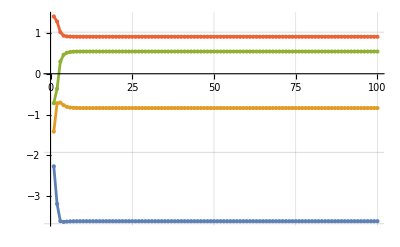

```mathematica
ListPlot[Map[Sort,Map[Diagonal,Data]]ᵀ,Joined->True,Mesh->All,
GridLines->{Automatic,Eigenvalues[A0]}]
```

```mathematica
A=A0;
Table[
α=Diagonal[A];
B = BDiaS[α,A];
{{λ},{v}}=Eigensystem[B,1];
Q=G4[v];
A=Q.A.Qᵀ,
{10}]
```

{{{1.60539,-0.250412,-0.20597,0.258118},{-0.250412,-1.78557,-0.252202,0.182212},{-0.20597,-0.252202,-1.19001,-0.250767},{0.258118,0.182212,-0.250767,1.4561}},{{1.77201,-0.212817,-0.210262,0.122348},{-0.212817,-1.88319,0.0306707,0.181317},{-0.210262,0.0306707,-1.09175,-0.272723},{0.122348,0.181317,-0.272723,1.28884}},{{1.78549,-0.187774,-0.207356,0.0993898},{-0.187774,-1.88113,0.0606762,0.187204},{-0.207356,0.0606762,-1.0928,-0.288311},{0.0993898,0.187204,-0.288311,1.27435}},{{1.78654,-0.186591,-0.206466,0.0975668},{-0.186591,-1.88063,0.0632598,0.188328},{-0.206466,0.0632598,-1.09326,-0.289021},{0.0975668,0.188328,-0.289021,1.27325}},{{1.78663,-0.186533,-0.206373,0.0974069},{-0.186533,-1.88057,0.0634996,0.188439},{-0.206373,0.0634996,-1.09331,-0.289054},{0.0974069,0.188439,-0.289054,1.27316}},{{1.78664,-0.18653,-0.206364,0.0973925},{-0.18653,-1.88057,0.0635216,0.188449},{-0.206364,0.0635216,-1.09332,-0.289056},{0.0973925,0.188449,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.0973912},{-0.186529,-1.88057,0.0635236,0.18845},{-0.206364,0.0635236,-1.09332,-0.289056},{0.0973912,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}},{{1.78664,-0.186529,-0.206364,0.097391},{-0.186529,-1.88057,0.0635238,0.18845},{-0.206364,0.0635238,-1.09332,-0.289056},{0.097391,0.18845,-0.289056,1.27315}}}